# Supernova outflow model : subsonic & supersonic outflows

This Mathematica notebook reproduces the results of the following paper https://arxiv.org/pdf/2009.10059

The goal is to solve the outflow equations which form a couple system of differential equations:

-Graphics-
where v is the outflow velocity, S is the entropy per baryon and qdot is a specific energy deposition rate. Moreover:
-Graphics-
These expressions taken into account the change in the effective number of relativistic degrees of freedom g_star, which occurs as the outflow cools through the temperature of the e+e- annihilation between the proton-neutron-star surface and the outer edges of the hot bubble. If one wants to neglect relativistic effects, the derivative of the logs is zero.

As the outflows accelerators to supersonic speeds and the sonic point (v = vs), being a mathematical singularity, requires some care. Next, one can use this wind solution up to the location of the termination shock. At this point, the density and velocity jump and the change in velocity at the termination shock is given by the Rankine-Hugoniot jump condition:
 -Graphics-
 where v1, T1, and S1 are the pre-shock quantities and therefore are taken from the wind solution at the location of the termination shock. 
 
 In this Mathematica notebook, we show how to calculate the subsonic and supersonic solutions, and how to find the velocity at the termination shock. For more details, we refer the reader to Ref https://arxiv.org/pdf/2009.10059 and in particular Figs. 2 and 4 for a one-to-one comparison between my results and those reported in that paper.

```mathematica
Clear["Global`*"];
```

#### Constants: G newton, solar mass, solar radius

```mathematica
constants=
{
G ->(6.67430*10^-11)*(10^-3)*(10^6) ,(* cm^3 g^-1 s^-2 *)
Msun ->1.989*10^33 ,(* g *)
Rsun->6.957*10^10 (* cm *)
}
```

{G→6.6743×10^-8,Msun→1.989×10^33,Rsun→6.957×10^10}

#### Parameters: velocity profile, mass of the supernova progenitor

```mathematica
parameters =
{v->v[r],
M->1.4 Msun}
```

{v→v[r],M→1.4 Msun}

#### Expressions for the speed of sound

```mathematica
vsrel={vs->√((Sf T)/(3 mN))}
```

{vs→(√((Sf T)/mN))/(√3)}

#### If entropy S is (roughly) constant, one can solve for T in the system of differential equations

```mathematica
condition=
{T-> mN/Sf(ϵf-v^2/2+ (G M)/r)}
```

{T→(mN ((G M)/r-v^2/2+ϵf))/Sf}

#### Differential equation describing the matter outflow in the supernova environment

```mathematica
EQ1 = (v-vs^2/v)^-1 ((2 vs^2)/r-(G M)/r^2)/.vsrel/.condition/.parameters/.constants/.{ϵf-> 2.321*10^18}
```

(-(1.85853×10^26)/r^2+(2 (2.321×10^18+(1.85853×10^26)/r-v[r]^2/2))/(3 r))/(v[r]-(2.321×10^18+(1.85853×10^26)/r-v[r]^2/2)/(3 v[r]))

#### Pre-critical solution: this corresponds to subsonic solutions of the outflow

```mathematica
ri=10^7;   (* initial radius in [cm] *)
rf=10^9;   (* final radius in [cm] *)
vi=5*10^8; (* initial velocity of outflow in [cm/s]; this velocity needs to be guessed: subsonic now *)

solpre=NDSolve[
{
(************** EQ1 **************)
v'[r]== EQ1,
v[ri]==vi
},
{v},{r,ri,rf}, AccuracyGoal->12,PrecisionGoal->12];
```

```mathematica
Post-critical solution:this corresponds to supernonic solutions of the outflow
```

```mathematica
ri=10^7; (* initial radius in [cm] *)
rf=10^9; (* initial radius in [cm] *)
vi=4.7036*10^9; (* initial velocity of outflow in [cm/s]; this velocity needs to be guessed: supersonic now *)

solpost=NDSolve[
{
(************** EQ1 **************)
v'[r]== EQ1,
v[ri]==vi
},
{v},{r,ri,rf}, AccuracyGoal->12,PrecisionGoal->12];
```

```mathematica
Plot the subsonic and supersonic solutions
```

```mathematica
LogLinearPlot[
Evaluate[{
v[r]/.solpre,
v[r]/.solpost
}],{r,ri,rf}, PlotRange->{{ri,rf},{0, 5*10^9}}, AxesLabel->{"r[cm]","v[cm/s]"}, PlotLabels->{"subsonic","supersonic"}]
```

-Graphics-

```mathematica
Plot physical solution realized by the outflow
```

Rcritical: critical radius i. e. radius at which the solution transitions from subsonic to supersonic

```mathematica
Rcritical=6*10^7;(* cm *)
Show[
LogLinearPlot[
Evaluate[{
v[r]/.solpre
}],{r,ri,Rcritical}, PlotRange->{{ri,rf},{0, 5*10^9}}, AxesLabel->{"r[cm]","v[cm/s]"}, PlotStyle->{Red},PlotLabels->{"Physical solution subsonic "}],
LogLinearPlot[
Evaluate[{
v[r]/.solpost
}],{r,Rcritical,rf}, PlotRange->{{ri,rf},{0, 5*10^9}}, AxesLabel->{"r[cm]","v[cm/s]"},PlotStyle->{Red}, PlotLabels->{"Physical solution supersonic"}]
]
```

-Graphics-

## Supersonic solution: extracting final velocity V1 pre-shock

V1 [cm/s] = 1.9461×10^9

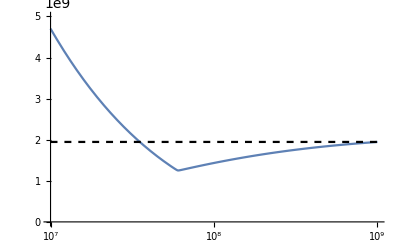

```mathematica
ri=10^7; (* cm *)
rf=10^9; (* cm *)
vi=4.7036*10^9; (* cm/s *)

ysol=NDSolveValue[
{
v'[r]== EQ1,
v[ri]==vi
},v,{r,ri,rf},AccuracyGoal->12,PrecisionGoal->12];
V1=ysol[rf];
Print["V1 [cm/s] = ", V1]

Show[
LogLinearPlot[{ysol[r]},{r,ri,rf},PlotRange->{{ri,rf},{0, 5*10^9}}],
LogLinearPlot[V1,{r,ri,rf}, PlotStyle->{Dashed,Black}]
]
```

## Rankine–Hugoniot conditions: find velocity V2 using V2 in the termination shock

```mathematica
ans=((2 T Sf/mN)+V1^2)/(7 V1^2)/.condition/.{v-> V1, r-> rf}/.parameters /.constants/.{ϵf-> 2.321*10^18} ;

Print["V2/V1 = ρ1/ρ2 = ", ans]
Print["_________________"]
Print["V1 = ",V1]
V2 = V1*ans;
Print["V2 = ", V2]
Print["_________________"]
```

V2/V1 = ρ1/ρ2 = 0.189118

_________________

V1 = 1.9461×10^9

V2 = 3.68041×10^8

_________________